```mathematica
SetDirectory[NotebookDirectory[]];
```

## Majorana fermion operators

```mathematica
(*
Chi(2i-1)=X(1) X(2) ... X(i-1) Z(i);
Chi(2i)=X(1)X(2)... X(i-1)Y(i);
{ Chi[i],Chi[j] }= 2 Delta_ij
*)
σ[0]={{1,0},{0,1}};
σ[1]={{0,1},{1,0}};
σ[2]={{0,-I},{I,0}};
σ[3]={{1,0},{0,-1}};

ProductZ[1]=σ[3];
ProductZ[i_]:=KroneckerProduct[ProductZ[i-1],σ[3]];

ProductI[1]=σ[0];
ProductI[i_]:=KroneckerProduct[ProductI[i-1],σ[0]];

ChiOdd[Ntot_,1]  :=KroneckerProduct[σ[1],ProductI[Ntot-1]];
ChiEven[Ntot_,1]:=KroneckerProduct[σ[2],ProductI[Ntot-1]];

ChiOdd[Ntot_,i_]:=KroneckerProduct[ProductZ[i-1],σ[1],ProductI[Ntot-i]];
ChiEven[Ntot_,i_]:=KroneckerProduct[ProductZ[i-1],σ[2],ProductI[Ntot-i]];

ChiOdd[Ntot_,Ntot_]:=KroneckerProduct[ProductZ[Ntot-1],σ[1]];
ChiEven[Ntot_,Ntot_]:=KroneckerProduct[ProductZ[Ntot-1],σ[2]];
```

## Ising Model

```mathematica
(nLtot+1)/nLtot//N
```

1.25

```mathematica
Clear[χ];
ntot=6; (* number of sites = 2*ntot *)
Ltot=2ntot;
For[i=1,i≤ntot,i=i+1,
χ[2i-1]=ChiOdd[ntot,i];
χ[2i]=ChiEven[ntot,i];
]
```

```mathematica
Table[χ[i].χ[j]+χ[j].χ[i]==IdentityMatrix[2^ntot]-IdentityMatrix[2^ntot],{i,1,2*ntot},{j,1,2*ntot}]//MatrixForm;
```

```mathematica
Table[χ[i].χ[j]+χ[j].χ[i]==2IdentityMatrix[2^ntot],{i,1,2*ntot},{j,1,2*ntot}]//MatrixForm;
```

```mathematica
Table[ConjugateTranspose[χ[i]]==χ[i],{i,1,2*ntot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[Conjugate[χ[i]]==χ[i],{i,1,2*ntot}]
```

{True,False,True,False,True,False,True,False,True,False,True,False}

```mathematica
Table[Transpose[χ[i]]==χ[i],{i,1,2*ntot}]
```

{True,False,True,False,True,False,True,False,True,False}

## Translation

```mathematica
Fn= 1/2 Sum[1- I* χ[2i-1].χ[2i],{i,1,ntot-1}];
TrnsG=IdentityMatrix[2^ntot];
For[i=1,i≤Ltot-1,i=i+1,
TrnsG=1/(√2)*TrnsG.(IdentityMatrix[2^ntot]-χ[i].χ[i+1])//Simplify;
]
TrnsNSNS=ⅇ^((2π*ⅈ*Ltot/2)/8)TrnsG;
Gf=IdentityMatrix[2^ntot];
For[i=1,i≤2ntot,i=i+1,
Gf=Gf.χ[i];
]
FP=(-ⅈ)^ntot*Gf;
```

```mathematica
TrnsNSNS.TrnsNSNS.TrnsNSNS.TrnsNSNS.TrnsNSNS.TrnsNSNS.TrnsNSNS.TrnsNSNS.TrnsNSNS.TrnsNSNS.FP;
```

```mathematica
Table[TrnsNSNS.χ[i].Inverse[TrnsNSNS]==χ[i+1],{i,1,2*ntot-1}]
```

{True,True,True,True,True,True,True,True,True}

```mathematica
TrnsNSNS.χ[Ltot].Inverse[TrnsNSNS]==-χ[1]
```

True

## Parity(flip ntot+l and ntot-l)

```mathematica
(*Pr=χ[ntot];
If[IntegerQ[ntot/2],
For[i=1,i≤ntot/2-1,i=i+1,
Pr=1/(√2)Pr.(χ[ntot+2i-1]-χ[ntot-2i+1]);
Pr=1/(√2)Pr.(χ[ntot+2i]+χ[ntot-2i])
];
Pr=1/(√2)Pr.(χ[2ntot-1]-χ[1]);
Pr=Pr.χ[2ntot];
];
If[IntegerQ[(ntot-1)/2 ],
For[i=1,i≤(ntot-1)/2,i=i+1,
Pr=1/(√2)Pr.(χ[ntot+2i-1]-χ[ntot-2i+1]);
Pr=1/(√2)Pr.(χ[ntot+2i]+χ[ntot-2i]);
];
];*)
```

```mathematica
(*Conjugate[Pr]-Pr;*)
```

```mathematica
(*Pr.Trns.Inverse[Pr]+Gf.Inverse[Trns]//Simplify;*)
```

```mathematica
(*Pr.Pr;*)
```

```mathematica
(*Pr.χ[ntot+3].Inverse[Pr]+χ[ntot-3]//MatrixForm;*)
```

```mathematica
(*Pr.Pr//MatrixForm;*)
```

## Parity2(flip l and 2ntot-l)

```mathematica
Pr=χ[2ntot];
If[IntegerQ[ntot/2],
For[i=1,i≤ntot/2-1,i=i+1,
Pr=1/(√2)Pr.(χ[2i-1]-χ[2ntot-2i+1]);
Pr=1/(√2)Pr.(χ[2i]+χ[2ntot-2i])
];
Pr=1/(√2)Pr.(χ[ntot-1]-χ[2ntot-ntot+1]);
Pr=Pr.χ[ntot];
PrG=Gf.χ[Ltot].Pr;
];
If[IntegerQ[(ntot-1)/2 ],
For[i=1,i≤(ntot-1)/2,i=i+1,
Pr=1/(√2)Pr.(χ[2i-1]-χ[2ntot-2i+1]);
Pr=1/(√2)Pr.(χ[2i]+χ[2ntot-2i]);
];
PrG=Gf.χ[Ltot].Pr;
];
PrG=(-1)^((ntot(ntot-1)(ntot-2))/2)ⅇ^((2π*ⅈ*ntot(ntot+1))/8)PrG;
```

```mathematica
PrG.χ[Ltot].Inverse[PrG]==-χ[Ltot]
```

True

```mathematica
PrG.χ[1].Inverse[PrG];
```

```mathematica
Table[PrG.χ[i].Inverse[PrG]==(-1)^i χ[2ntot-i],{i,1,2*ntot-1}]
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
PrG.PrG//MatrixForm;
```

```mathematica
PrG.TrnsNSNS.Inverse[PrG]-(-1)^ntot Gf.Inverse[TrnsNSNS]//Simplify;
```

```mathematica
PrG.TrnsNSNS.Inverse[PrG]-Gf.Inverse[TrnsNSNS];
```

```mathematica
PrG.TrnsNSNS.Inverse[PrG]==(-1)^ntot Gf.Inverse[TrnsNSNS]
```

True

```mathematica
m=-0.0;
```

```mathematica
Hkit=(- I)/2 * Sum[ χ[i].χ[i+1],{i,1,Ltot-1}]+I/2*χ[Ltot].χ[1]-I/2 *m* Sum[ (-1)^i χ[i].χ[i+1],{i,1,Ltot-1}]+ I/2*m*(-1)^Ltot χ[Ltot].χ[1]-100*IdentityMatrix[2^ntot];
```

```mathematica
HkitES=Eigenvalues[Hkit]//Sort
```

{-103.864,-103.346,-103.346,-102.828,-102.449,-102.449,-101.932,-101.932,-101.932,-101.932,-101.932,-101.932,-101.414,-101.414,-101.414,-101.414,-101.414,-101.414,-101.035,-100.897,-100.897,-100.518,-100.518,-100.518,-100.518,-100.518,-100.518,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-99.4824,-99.4824,-99.4824,-99.4824,-99.4824,-99.4824,-99.1034,-99.1034,-98.9647,-98.5858,-98.5858,-98.5858,-98.5858,-98.5858,-98.5858,-98.0681,-98.0681,-98.0681,-98.0681,-98.0681,-98.0681,-97.5505,-97.5505,-97.1716,-96.6539,-96.6539,-96.1363}

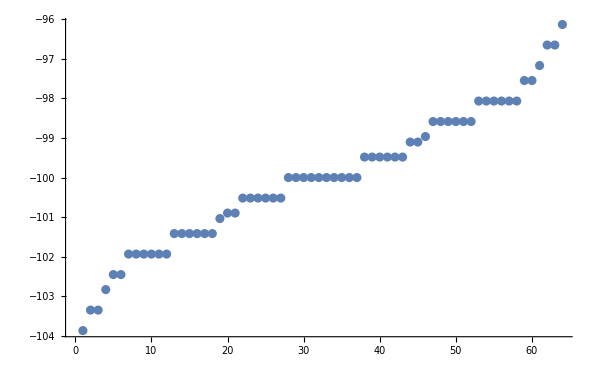

```mathematica
ListPlot[Eigenvalues[Hkit]//Sort,PlotRange->All]
```

```mathematica
TrnsNSNS.Hkit.Inverse[TrnsNSNS]-Hkit//Simplify//MatrixForm
```

```mathematica
HkitEigen=Eigensystem[Hkit];
```

```mathematica
Trans2Ev=Table[Conjugate[HkitEigen⟦2,i⟧].TrnsNSNS.TrnsNSNS.HkitEigen⟦2,i⟧,{i,1,Ltot}]
```

{1.+0. ⅈ,0.866025+0. ⅈ,0.866025+0. ⅈ,1.+0. ⅈ,1.11022×10^-16+0. ⅈ,1.38778×10^-16+0. ⅈ,0.113009+0. ⅈ,-0.631742+0. ⅈ,-0.310398+0. ⅈ,-0.58556+0. ⅈ,-0.316423+0. ⅈ,-0.000937174+0. ⅈ}

```mathematica
ComplexListPlot[Trans2Ev];
```

```mathematica
Table[Conjugate[HkitEigen⟦2,i⟧].TrnsNSNS.TrnsNSNS.HkitEigen⟦2,i⟧,{i,1,Ltot}]
```

{1.+0. ⅈ,0.92388+0. ⅈ,0.92388+0. ⅈ,1.+0. ⅈ,0.382683+0. ⅈ,0.382683+0. ⅈ,0.420592+0. ⅈ,0.6016+0. ⅈ,0.136367+0. ⅈ,0.255654+0. ⅈ,-0.382683+0. ⅈ,-0.382683+0. ⅈ,0.382683+0. ⅈ,0.382683+0. ⅈ,-0.92388+0. ⅈ,-0.92388+0. ⅈ}

```mathematica
Corχ=Table[Re[-ⅈ*Conjugate[HkitES⟦2,1⟧].χ[2i].χ[1].HkitES⟦2,1⟧],{i,1,ntot}];
```

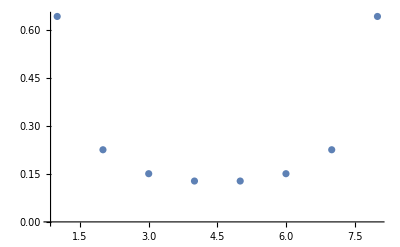

```mathematica
ListPlot[Corχ,PlotRange->All]
```

```mathematica
Fn= 1/2 Sum[1- I* χ[2i-1].χ[2i],{i,1,ntot-1}];
```

```mathematica
(Hkit.Fn-Fn.Hkit).(Hkit.Fn-Fn.Hkit)//Simplify;
```

```mathematica
m=-0.001;
```

```mathematica
HkitMod=(- I)/2 * Sum[1/π Sin[π/Ltot*i] χ[i].χ[i+1],{i,1,Ltot-1}]- I/2 *m* Sum[ 1/π Sin[π/Ltot*i]*(-1)^i χ[i].χ[i+1],{i,1,Ltot-1}];
```

```mathematica
HkitModEigen=Eigensystem[HkitMod];
```

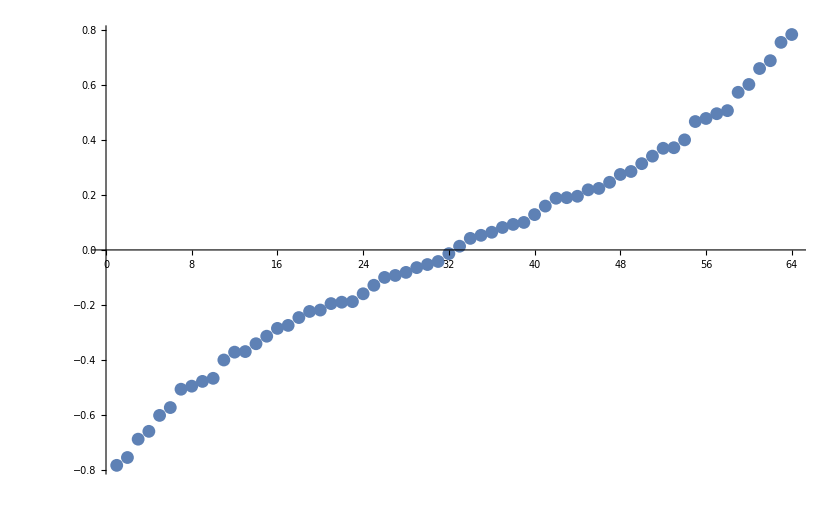

```mathematica
ListPlot[Eigenvalues[HkitMod]//Sort,PlotRange->All]
```

## Lattice CRT

```mathematica
Table[TrnsNSNS.PrG.Conjugate[χ[i]].Inverse[PrG].Inverse[TrnsNSNS]==-χ[Ltot-i+1],{i,1,2*ntot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[PrG.Inverse[TrnsNSNS].Conjugate[χ[i]].TrnsNSNS.Inverse[PrG]==χ[Ltot-i+1],{i,1,2*ntot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
FP.TrnsNSNS.PrG==PrG.Inverse[TrnsNSNS]
```

True

```mathematica
ResCRTNSNS=FP.TrnsNSNS.PrG.Conjugate[Hkit].Inverse[PrG].Inverse[TrnsNSNS].Inverse[FP]-Hkit;
```

```mathematica
Tr[ResCRTNSNS.ConjugateTranspose[ResCRTNSNS]]
```

2.16164×10^-26+0. ⅈ

## Infinite T TFD

```mathematica
StabF=- I * Sum[ χ[i].χ[Ltot-i+1],{i,1,ntot}]-100*IdentityMatrix[2^ntot];
```

```mathematica
TFDIT=Eigensystem[StabF]⟦2,1⟧
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
TrnsNSNS.PrG.Conjugate[StabF].Inverse[PrG].Inverse[TrnsNSNS]==StabF
```

True

```mathematica
Up2=MatrixPower[TrnsNSNS,ntot/2];
```

```mathematica
Up2.Up2.Up2.Up2//MatrixForm;
```

```mathematica
FP.TrnsNSNS.PrG.Conjugate[Up2.StabF.Inverse[Up2]].Inverse[PrG].Inverse[TrnsNSNS].Inverse[FP]==Up2.StabF.Inverse[Up2]
```

True

```mathematica
A=Inverse[Up2].FP.TrnsNSNS.PrG.Conjugate[Up2.χ[1].Inverse[Up2]].Inverse[PrG].Inverse[TrnsNSNS].Inverse[FP].Up2;
```

## Modular Hamiltonian

```mathematica
Clear[χL];
nLtot=ntot/2; (* number of sites = 2*ntot *)
LLtot=2nLtot;
For[i=1,i≤nLtot,i=i+1,
χL[2i-1]=ChiOdd[nLtot,i];
χL[2i]=ChiEven[nLtot,i];
]
```

## Translation

```mathematica
FnL= 1/2 Sum[IdentityMatrix[2^nLtot]- I* χL[2i-1].χL[2i],{i,1,nLtot-1}];
TrnsGL=IdentityMatrix[2^nLtot];
For[i=1,i≤LLtot-1,i=i+1,
TrnsGL=1/(√2)*TrnsGL.(IdentityMatrix[2^nLtot]-χL[i].χL[i+1])//Simplify;
]
TrnsNSNSL=ⅇ^((2π*ⅈ*nLtot)/8)TrnsGL;
GfL=IdentityMatrix[2^nLtot];
For[i=1,i≤2nLtot,i=i+1,
GfL=GfL.χL[i];
]
FPL=(-ⅈ)^nLtot*GfL;
```

## Parity2(flip l and 2ntot-l)

```mathematica
PrL=χL[2nLtot];
(*If[IntegerQ[nLtot/2]=2,
PrL=1/(√2)PrL.(χL[nLtot-1]-χL[2nLtot-nLtot+1]);
PrL=PrL.χL[nLtot];
];*)
If[IntegerQ[nLtot/2],
For[i=1,i≤nLtot/2-1,i=i+1,
PrL=1/(√2)PrL.(χL[2i-1]-χL[2nLtot-2i+1]);
PrL=1/(√2)PrL.(χL[2i]+χL[2nLtot-2i])
];
PrL=1/(√2)PrL.(χL[nLtot-1]-χL[2nLtot-nLtot+1]);
PrL=PrL.χL[nLtot];
PrGL=GfL.χL[LLtot].PrL;
];
If[IntegerQ[(nLtot-1)/2 ],
For[i=1,i≤(nLtot-1)/2,i=i+1,
PrL=1/(√2)PrL.(χL[2i-1]-χL[2nLtot-2i+1]);
PrL=1/(√2)PrL.(χL[2i]+χL[2nLtot-2i]);
PrGL=GfL.χL[LLtot].PrL;
];
];
PrGL=(-1)^((nLtot(nLtot-1)(nLtot-2))/2)ⅇ^((2π*ⅈ*nLtot(nLtot+1))/8)PrGL;
```

```mathematica
PrGL
```

{{1/2,0,0,1/2,0,1/2,1/2,0},{0,-1/2,-1/2,0,-1/2,0,0,-1/2},{0,-1/2,-1/2,0,1/2,0,0,1/2},{1/2,0,0,1/2,0,-1/2,-1/2,0},{0,-1/2,1/2,0,1/2,0,0,-1/2},{1/2,0,0,-1/2,0,-1/2,1/2,0},{1/2,0,0,-1/2,0,1/2,-1/2,0},{0,-1/2,1/2,0,-1/2,0,0,1/2}}

```mathematica
PrL.χL[LLtot].Inverse[PrL]-χL[LLtot];
```

```mathematica
PrGL.PrGL;
```

```mathematica
PrGL.TrnsNSNSL.Inverse[PrGL]-(-1)^nLtot GfL.Inverse[TrnsNSNSL]//Simplify;
```

```mathematica
PrGL.TrnsNSNSL.Inverse[PrGL]-FPL.Inverse[TrnsNSNSL]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Table[PrGL.TrnsNSNSL.Inverse[PrGL]==FPL.Inverse[TrnsNSNSL],{i,1,1}]
```

{True}

```mathematica
m=-0.01;
```

```mathematica
HkitL=(- I)/2 * Sum[ χL[i].χL[i+1],{i,1,LLtot-1}]+I/2*χL[LLtot].χL[1]-I/2 *m* Sum[ (-1)^i χL[i].χL[i+1],{i,1,LLtot-1}]+ I/2*m*(-1)^LLtot χL[LLtot].χL[1];
```

```mathematica
Eigenvalues[HkitL]
```

{2.00015,-2.00015,-1.,1.,1.,-1.,-0.000149989,0.000149989}

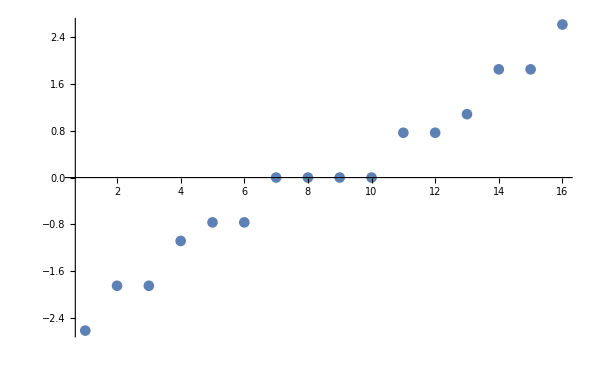

```mathematica
ListPlot[Eigenvalues[HkitL]//Sort,PlotRange->All]
```

```mathematica
TrnsNSNSL.HkitL.Inverse[TrnsNSNSL]-HkitL//Simplify//MatrixForm;
```

```mathematica
m=-0.000001;
```

```mathematica
HkitModL=(- I)/2 * Sum[Ltot/π Sin[π/LLtot*i] χL[i].χL[i+1],{i,1,LLtot-1}]- I/2 *m* Sum[ Ltot/π Sin[π/LLtot*i]*(-1)^i χL[i].χL[i+1],{i,1,LLtot-1}];
```

```mathematica
HkitModLEigen=Eigensystem[HkitModL];
```

```mathematica
HkitModLEigen⟦2,4⟧
```

{0.250254+0. ⅈ,2.5902×10^-16+0. ⅈ,-1.11022×10^-16+0. ⅈ,-0.590382+0. ⅈ,-1.8536×10^-17+0. ⅈ,0.490176+0. ⅈ,-0.590382+0. ⅈ,0.+0. ⅈ}

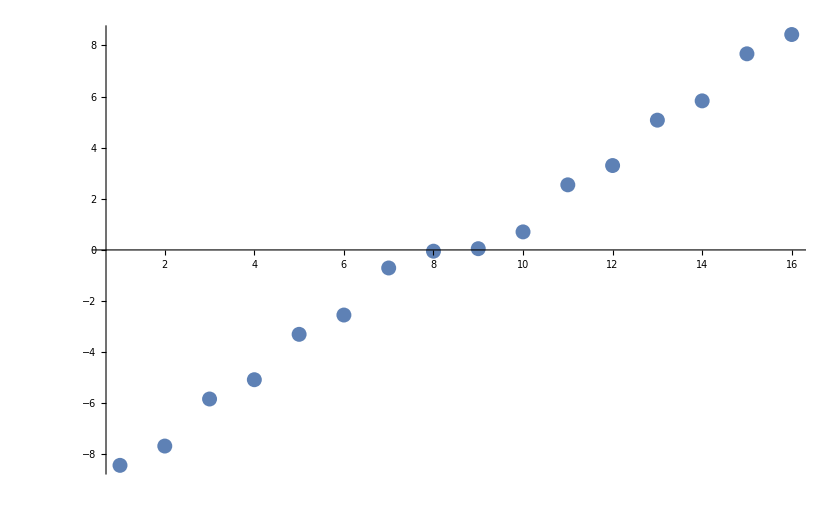

```mathematica
ListPlot[Eigenvalues[HkitModL]//Sort,PlotRange->All]
```

## Lattice CRTL

```mathematica
Table[FPL.TrnsNSNSL.PrGL.Conjugate[χL[i]].Inverse[PrGL].Inverse[TrnsNSNSL].Inverse[FPL]==χL[LLtot-i+1],{i,1,2*nLtot}]
```

{True,True,True,True,True,True}

```mathematica
TrnsGL.PrGL.HkitModL.Inverse[PrGL].Inverse[TrnsGL];
```

```mathematica
Res=TrnsGL.PrGL.Conjugate[HkitModL].Inverse[PrGL].Inverse[TrnsGL]-HkitModL;
```

```mathematica
Tr[Res.ConjugateTranspose[Res]]
```

2.21478×10^-30-4.03873×10^-49 ⅈ

```mathematica
Sum[KroneckerProduct[HkitModLEigen⟦2,i⟧,FPL.TrnsNSNSL.PrGL.Conjugate[HkitModLEigen⟦2,i⟧]],{i,1,2^nLtot}]//MatrixForm
```

(1.-1.11022×10^-16 ⅈ | -6.3232×10^-33-5.69543×10^-17 ⅈ | 2.49955×10^-33+2.2514×10^-17 ⅈ | -2.77556×10^-17+3.08149×10^-33 ⅈ | 2.26019×10^-33+2.0358×10^-17 ⅈ | 2.77556×10^-17+0. ⅈ | -5.55112×10^-17+3.08149×10^-33 ⅈ | 0.+0. ⅈ
2.0358×10^-17-2.26019×10^-33 ⅈ | 6.16298×10^-33+5.55112×10^-17 ⅈ | -6.16298×10^-33-5.55112×10^-17 ⅈ | 5.01365×10^-17-5.56627×10^-33 ⅈ | 1.11022×10^-16+1. ⅈ | 6.10024×10^-17-6.77263×10^-33 ⅈ | -2.04851×10^-16+2.2743×10^-32 ⅈ | -3.08149×10^-33+0. ⅈ
2.2514×10^-17-2.49955×10^-33 ⅈ | -6.16298×10^-33-5.55112×10^-17 ⅈ | 1.11022×10^-16+1. ⅈ | -3.33921×10^-17+3.70727×10^-33 ⅈ | -6.16298×10^-33-5.55112×10^-17 ⅈ | -4.41346×10^-17+4.89993×10^-33 ⅈ | -1.21993×10^-17+1.3544×10^-33 ⅈ | 1.2326×10^-32+5.55112×10^-17 ⅈ
-2.77556×10^-17+3.08149×10^-33 ⅈ | 3.12253×10^-32+2.81253×10^-16 ⅈ | -1.3544×10^-33-1.21993×10^-17 ⅈ | 2.35922×10^-16-2.92741×10^-32 ⅈ | -2.2743×10^-32-2.04851×10^-16 ⅈ | 1.80411×10^-16-1.77186×10^-32 ⅈ | 1.-1.11022×10^-16 ⅈ | 0.+0. ⅈ
-5.69543×10^-17+6.3232×10^-33 ⅈ | 1.11022×10^-16+1. ⅈ | -6.16298×10^-33-5.55112×10^-17 ⅈ | -3.10533×10^-16+3.44761×10^-32 ⅈ | 6.16298×10^-33+5.55112×10^-17 ⅈ | -9.51017×10^-17+1.05584×10^-32 ⅈ | 2.81253×10^-16-3.12253×10^-32 ⅈ | -3.08149×10^-33+0. ⅈ
0.+0. ⅈ | -1.05584×10^-32-9.51017×10^-17 ⅈ | -4.89993×10^-33-4.41346×10^-17 ⅈ | 1.8735×10^-16-2.23408×10^-32 ⅈ | 6.77263×10^-33+6.10024×10^-17 ⅈ | 1.-1.11022×10^-16 ⅈ | 1.80411×10^-16-1.77186×10^-32 ⅈ | 0.+0. ⅈ
0.+3.08149×10^-33 ⅈ | -3.44761×10^-32-3.10533×10^-16 ⅈ | -3.70727×10^-33-3.33921×10^-17 ⅈ | 1.-1.11022×10^-16 ⅈ | 5.56627×10^-33+5.01365×10^-17 ⅈ | 2.22045×10^-16-2.23408×10^-32 ⅈ | 2.35922×10^-16-2.92741×10^-32 ⅈ | -2.36126×10^-33-2.12684×10^-17 ⅈ
0.+0. ⅈ | -3.08149×10^-33+0. ⅈ | 1.2326×10^-32+6.93889×10^-17 ⅈ | -2.12684×10^-17+2.36126×10^-33 ⅈ | -3.08149×10^-33+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.11022×10^-16+1. ⅈ)

```mathematica
HkitModLEigen⟦2⟧//Length
```

8

## Lattice CRTL

```mathematica
ModETens=Table[Flatten[KroneckerProduct[HkitModLEigen⟦2,i⟧,FPL.TrnsNSNSL.PrGL.Conjugate[HkitModLEigen⟦2,i⟧]]],{i,1,2^nLtot}];(*List of |E_L>|CRTl E_R>*)
```

```mathematica
KroneckerProduct[HkitModLEigen⟦2,1⟧,TrnsNSNSL.PrGL.Conjugate[HkitModLEigen⟦2,1⟧]];
```

```mathematica
HkitES=Eigensystem[Hkit];
```

```mathematica
HkitES⟦1,1⟧
```

-103.864

```mathematica
HkitES⟦2,1⟧;
```

```mathematica
ModETens⟦1⟧
```

{0.820989-9.11481×10^-17 ⅈ,-1.90382×10^-32-1.7148×10^-16 ⅈ,5.58418×10^-33+5.02978×10^-17 ⅈ,0.2437-2.70561×10^-17 ⅈ,1.16748×10^-32+1.05157×10^-16 ⅈ,0.16789-1.86396×10^-17 ⅈ,0.2437-2.70561×10^-17 ⅈ,0.+0. ⅈ,1.05157×10^-16-1.16748×10^-32 ⅈ,-2.43853×10^-48-2.19643×10^-32 ⅈ,7.15256×10^-49+6.44245×10^-33 ⅈ,3.12145×10^-17-3.46551×10^-33 ⅈ,1.49538×10^-48+1.34692×10^-32 ⅈ,2.15044×10^-17-2.38747×10^-33 ⅈ,3.12145×10^-17-3.46551×10^-33 ⅈ,0.+0. ⅈ,5.02978×10^-17-5.58418×10^-33 ⅈ,-1.16637×10^-48-1.05057×10^-32 ⅈ,3.42114×10^-49+3.08149×10^-33 ⅈ,1.49302×10^-17-1.65759×10^-33 ⅈ,7.15256×10^-49+6.44245×10^-33 ⅈ,1.02858×10^-17-1.14195×10^-33 ⅈ,1.49302×10^-17-1.65759×10^-33 ⅈ,0.+0. ⅈ,0.2437-2.70561×10^-17 ⅈ,-5.65122×10^-33-5.09017×10^-17 ⅈ,1.65759×10^-33+1.49302×10^-17 ⅈ,0.0723389-8.03123×10^-18 ⅈ,3.46551×10^-33+3.12145×10^-17 ⅈ,0.049836-5.53291×10^-18 ⅈ,0.0723389-8.03123×10^-18 ⅈ,0.+0. ⅈ,-1.7148×10^-16+1.90382×10^-32 ⅈ,3.97651×10^-48+3.58172×10^-32 ⅈ,-1.16637×10^-48-1.05057×10^-32 ⅈ,-5.09017×10^-17+5.65122×10^-33 ⅈ,-2.43853×10^-48-2.19643×10^-32 ⅈ,-3.50674×10^-17+3.89326×10^-33 ⅈ,-5.09017×10^-17+5.65122×10^-33 ⅈ,0.+0. ⅈ,0.16789-1.86396×10^-17 ⅈ,-3.89326×10^-33-3.50674×10^-17 ⅈ,1.14195×10^-33+1.02858×10^-17 ⅈ,0.049836-5.53291×10^-18 ⅈ,2.38747×10^-33+2.15044×10^-17 ⅈ,0.0343332-3.81175×10^-18 ⅈ,0.049836-5.53291×10^-18 ⅈ,0.+0. ⅈ,0.2437-2.70561×10^-17 ⅈ,-5.65122×10^-33-5.09017×10^-17 ⅈ,1.65759×10^-33+1.49302×10^-17 ⅈ,0.0723389-8.03123×10^-18 ⅈ,3.46551×10^-33+3.12145×10^-17 ⅈ,0.049836-5.53291×10^-18 ⅈ,0.0723389-8.03123×10^-18 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
ModETens⟦4⟧
```

{0.062627-6.95299×10^-18 ⅈ,-5.14998×10^-34-4.63869×10^-18 ⅈ,-3.08462×10^-33-2.77838×10^-17 ⅈ,-0.147745+1.6403×10^-17 ⅈ,7.19654×10^-33+6.48207×10^-17 ⅈ,0.122668-1.36189×10^-17 ⅈ,-0.147745+1.6403×10^-17 ⅈ,0.+0. ⅈ,6.48207×10^-17-7.19654×10^-33 ⅈ,-5.33038×10^-49-4.80118×10^-33 ⅈ,-3.19267×10^-48-2.8757×10^-32 ⅈ,-1.52921×10^-16+1.69776×10^-32 ⅈ,7.44863×10^-48+6.70913×10^-32 ⅈ,1.26965×10^-16-1.4096×10^-32 ⅈ,-1.52921×10^-16+1.69776×10^-32 ⅈ,0.+0. ⅈ,-2.77838×10^-17+3.08462×10^-33 ⅈ,2.28473×10^-49+2.0579×10^-33 ⅈ,1.36846×10^-48+1.2326×10^-32 ⅈ,6.55455×10^-17-7.27701×10^-33 ⅈ,-3.19267×10^-48-2.8757×10^-32 ⅈ,-5.44204×10^-17+6.04188×10^-33 ⅈ,6.55455×10^-17-7.27701×10^-33 ⅈ,0.+0. ⅈ,-0.147745+1.6403×10^-17 ⅈ,1.21495×10^-33+1.09433×10^-17 ⅈ,7.27701×10^-33+6.55455×10^-17 ⅈ,0.34855-3.86969×10^-17 ⅈ,-1.69776×10^-32-1.52921×10^-16 ⅈ,-0.289391+3.21288×10^-17 ⅈ,0.34855-3.86969×10^-17 ⅈ,0.+0. ⅈ,-4.63869×10^-18+5.14998×10^-34 ⅈ,3.81452×10^-50+3.43582×10^-34 ⅈ,2.28473×10^-49+2.0579×10^-33 ⅈ,1.09433×10^-17-1.21495×10^-33 ⅈ,-5.33038×10^-49-4.80118×10^-33 ⅈ,-9.08588×10^-18+1.00873×10^-33 ⅈ,1.09433×10^-17-1.21495×10^-33 ⅈ,0.+0. ⅈ,0.122668-1.36189×10^-17 ⅈ,-1.00873×10^-33-9.08588×10^-18 ⅈ,-6.04188×10^-33-5.44204×10^-17 ⅈ,-0.289391+3.21288×10^-17 ⅈ,1.4096×10^-32+1.26965×10^-16 ⅈ,0.240272-2.66756×10^-17 ⅈ,-0.289391+3.21288×10^-17 ⅈ,0.+0. ⅈ,-0.147745+1.6403×10^-17 ⅈ,1.21495×10^-33+1.09433×10^-17 ⅈ,7.27701×10^-33+6.55455×10^-17 ⅈ,0.34855-3.86969×10^-17 ⅈ,-1.69776×10^-32-1.52921×10^-16 ⅈ,-0.289391+3.21288×10^-17 ⅈ,0.34855-3.86969×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
HkitES⟦1⟧
```

{-103.864,-103.346,-103.346,-102.828,-102.449,-102.449,-101.932,-101.932,-101.932,-101.932,-101.932,-101.932,-101.414,-101.414,-101.414,-101.414,-101.414,-101.414,-101.035,-100.897,-100.897,-100.518,-100.518,-100.518,-100.518,-100.518,-100.518,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-100.,-99.4824,-99.4824,-99.4824,-99.4824,-99.4824,-99.4824,-99.1034,-99.1034,-98.9647,-98.5858,-98.5858,-98.5858,-98.5858,-98.5858,-98.5858,-98.0681,-98.0681,-98.0681,-98.0681,-98.0681,-98.0681,-97.5505,-97.5505,-97.1716,-96.6539,-96.6539,-96.1363}

```mathematica
HkitES⟦2,1⟧;(*Ground state*)
```

```mathematica
(*ⅇ^(ⅈ/4 π)*)Table[Conjugate[ModETens⟦i⟧].HkitES⟦2,1⟧,{i,1,2^nLtot}]
```

{0.866498-9.05429×10^-31 ⅈ,1.01685×10^-6-2.58791×10^-32 ⅈ,5.4987×10^-33+1.8296×10^-6 ⅈ,-3.47001×10^-31+0.481583 ⅈ,2.3054×10^-33+7.7386×10^-6 ⅈ,-2.24586×10^-31+0.113858 ⅈ,0.0000139238+1.37528×10^-33 ⅈ,0.0632802-4.56161×10^-31 ⅈ,-1.52053×10^-32+0.0000597242 ⅈ,-5.49533×10^-33+0.0147529 ⅈ,0.00010746+1.66141×10^-32 ⅈ,0.00819935+4.66054×10^-32 ⅈ,0.00193853+1.13972×10^-31 ⅈ,0.000454521+3.03079×10^-32 ⅈ,6.5533×10^-33+0.000817806 ⅈ,7.31433×10^-32+0.0010774 ⅈ}

```mathematica
PhaseVecG=(*ⅇ^(ⅈ/4 π)*)Table[(Conjugate[ModETens⟦i⟧].HkitES⟦2,1⟧)/Abs[Conjugate[ModETens⟦i⟧].HkitES⟦2,1⟧],{i,1,2^nLtot}]
```

{1.-1.04493×10^-30 ⅈ,1.-2.54501×10^-26 ⅈ,3.00542×10^-27+1. ⅈ,-7.20543×10^-31+1. ⅈ,2.97909×10^-28+1. ⅈ,-1.97251×10^-30+1. ⅈ,1.+9.87715×10^-29 ⅈ,1.-7.20859×10^-30 ⅈ,-2.54591×10^-28+1. ⅈ,-3.72492×10^-31+1. ⅈ,1.+1.54608×10^-28 ⅈ,1.+5.68403×10^-30 ⅈ,1.+5.87928×10^-29 ⅈ,1.+6.6681×10^-29 ⅈ,8.01327×10^-30+1. ⅈ,6.78889×10^-29+1. ⅈ}

```mathematica
Table[Conjugate[HkitModLEigen⟦2,i⟧].FPL.HkitModLEigen⟦2,i⟧,{i,1,2^nLtot}]
```

{1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ}

```mathematica
Sum[Conjugate[ModETens⟦i⟧].HkitES⟦2,1⟧*ModETens⟦i⟧.Conjugate[HkitES⟦2,1⟧],{i,1,2^nLtot}]//N
```

1.+0. ⅈ

```mathematica
(*ⅇ^(ⅈ/4 π)*)Table[Conjugate[ModETens⟦i⟧].TFDIT,{i,1,2^nLtot}]
```

{1.-1.33133×10^-32 ⅈ,1.-2.03219×10^-31 ⅈ,1.72945×10^-31-1. ⅈ,7.53087×10^-32-1. ⅈ,1.72551×10^-31-1. ⅈ,1.44179×10^-31-1. ⅈ,1.-1.11843×10^-32 ⅈ,1.-7.37106×10^-32 ⅈ,2.34456×10^-30-1. ⅈ,5.16245×10^-31-1. ⅈ,1.-8.71055×10^-30 ⅈ,1.-6.17131×10^-30 ⅈ,1.-1.0701×10^-31 ⅈ,1.-2.93409×10^-31 ⅈ,1.64439×10^-30-1. ⅈ,2.67932×10^-30-1. ⅈ}

```mathematica
PhaseVecTFD=Table[(Conjugate[ModETens⟦i⟧].TFDIT)/Abs[Conjugate[ModETens⟦i⟧].TFDIT],{i,1,2^nLtot}]
```

{1.-1.33133×10^-32 ⅈ,1.-2.03219×10^-31 ⅈ,1.72945×10^-31-1. ⅈ,7.53087×10^-32-1. ⅈ,1.72551×10^-31-1. ⅈ,1.44179×10^-31-1. ⅈ,1.-1.11843×10^-32 ⅈ,1.-7.37106×10^-32 ⅈ,2.34456×10^-30-1. ⅈ,5.16245×10^-31-1. ⅈ,1.-8.71055×10^-30 ⅈ,1.-6.17131×10^-30 ⅈ,1.-1.0701×10^-31 ⅈ,1.-2.93409×10^-31 ⅈ,1.64439×10^-30-1. ⅈ,2.67932×10^-30-1. ⅈ}

## Modular Energy (Entanglement Spectrum)

```mathematica
ModE=Table[-1/2 Log[Conjugate[ModETens⟦i⟧].HkitES⟦2,1⟧*ModETens⟦i⟧.Conjugate[HkitES⟦2,1⟧]],{i,1,2^nLtot}]//Sort
```

{0.143295+0. ⅈ,0.730677+0. ⅈ,2.1728+0. ⅈ,2.76018+0. ⅈ,4.21632+0. ⅈ,4.8037+0. ⅈ,6.24582+0. ⅈ,6.83321+0. ⅈ,7.10889+0. ⅈ,7.69627+0. ⅈ,9.13839+0. ⅈ,9.72577+0. ⅈ,11.1819+0. ⅈ,11.7693+0. ⅈ,13.2114+0. ⅈ,13.7988+0. ⅈ}

```mathematica
ModEshift=ModE-1/2(ModE⟦1⟧+ModE⟦2^nLtot⟧)
```

{-6.82775+0. ⅈ,-6.24037+0. ⅈ,-4.79824+0. ⅈ,-4.21086+0. ⅈ,-2.75473+0. ⅈ,-2.16735+0. ⅈ,-0.725221+0. ⅈ,-0.137839+0. ⅈ,0.137839+0. ⅈ,0.725221+0. ⅈ,2.16735+0. ⅈ,2.75473+0. ⅈ,4.21086+0. ⅈ,4.79824+0. ⅈ,6.24037+0. ⅈ,6.82775+0. ⅈ}

```mathematica
DefEn=Eigenvalues[HkitModL]//Sort;
DefEnNorm=(ModEshift⟦2^nLtot⟧-ModEshift⟦1⟧)/(DefEn⟦2^nLtot⟧-DefEn⟦1⟧)DefEn;
```

```mathematica
Eigenvalues[HkitModL]
```

{-4.80165,4.80165,3.98421,-3.98421,1.90986,-1.90986,-1.09243,1.09243}

```mathematica
1.7159969261845645/2.2053163167933425*1.273238271495618/1.009043469909752
```

0.981851

```mathematica
3.8452352943528494/4.801648756577113
```

0.800816

```mathematica
Ra=6.827751297076589/8.426275476897139//N
```

0.810293

```mathematica
π^2/8//N
```

1.2337

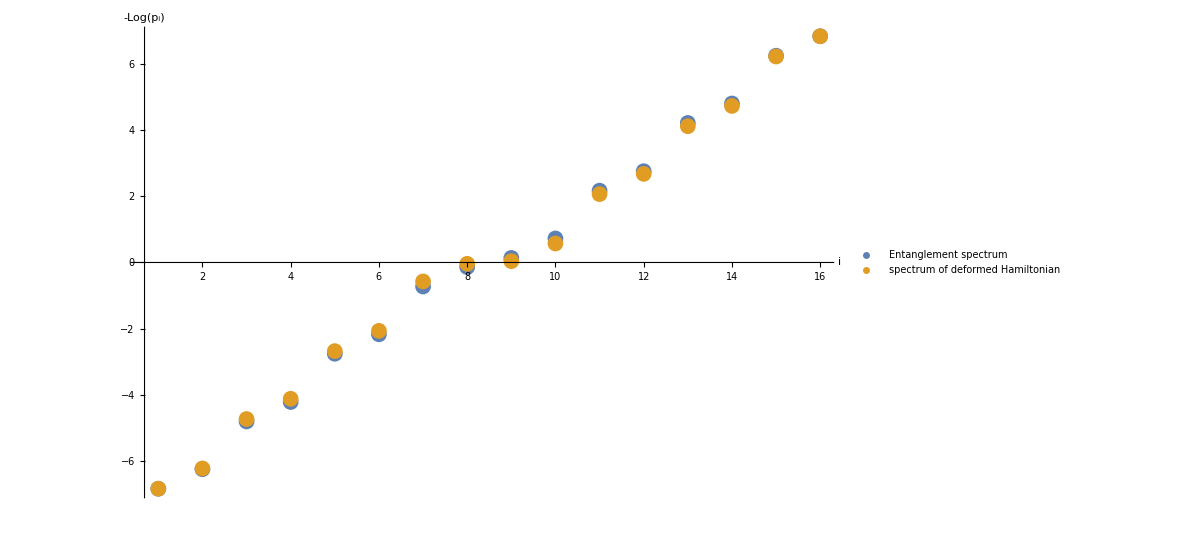

```mathematica
ModEvsConfMod=ListPlot[{ModEshift,DefEnNorm},PlotRange->All,TicksStyle->Directive[Black,12],PlotLegends->Placed[{Style["Entanglement spectrum",FontSize->12,Black],Style["spectrum of deformed Hamiltonian",FontSize->12,Black]},{Scaled[{0.35,0.85}],{0.5,0.4}}],AxesLabel->{Style["i",FontSize->16,Black],Style["-Log(p_i)",FontSize->16,Black]}](*May be Yifan Liu, Atsushi Ueda paper mension this*)
```

```mathematica
Export["ModEvsConfMod.pdf",ModEvsConfMod]
```

ModEvsConfMod.pdf

```mathematica
FLlist=Table[Conjugate[HkitModLEigen⟦2,i⟧].FPL.HkitModLEigen⟦2,i⟧,{i,1,2^nLtot}];
```

```mathematica
TFDIsing[β_,θ_]=Sum[Exp[-β/2(HkitModLEigen⟦1,j⟧)]*Exp[ⅈ*θ/2*(1-FLlist⟦j⟧)]*(Conjugate[ModETens⟦j⟧].HkitES⟦2,1⟧)/Abs[Conjugate[ModETens⟦j⟧].HkitES⟦2,1⟧]*ModETens⟦j⟧,{j,1,2^nLtot}];
TFDIsingC[β_,θ_]=Sum[Exp[-β/2(HkitModLEigen⟦1,j⟧)]*Exp[-ⅈ*θ/2*(1-FLlist⟦j⟧)]*Conjugate[(Conjugate[ModETens⟦j⟧].HkitES⟦2,1⟧)/Abs[Conjugate[ModETens⟦j⟧].HkitES⟦2,1⟧]]*Conjugate[ModETens⟦j⟧],{j,1,2^nLtot}];
```

```mathematica
OverlapIsing[β_,θ_]=(Conjugate[HkitES⟦2,1⟧].TFDIsing[β,θ]*TFDIsingC[β,θ].HkitES⟦2,1⟧)/(TFDIsingC[β,θ].TFDIsing[β,θ]);
dOverlapIsing[β_,θ_]=D[OverlapIsing[β], β];
```

```mathematica
βmin=0.1//N;
βmax=50//N;
Do[
βt=1/2(βmin+βmax);
If[Re[dOverlapIsing[βt,0]]>0,
βmin=1/2(βmin+βmax),
];
If[Re[dOverlapIsing[βt,0]]<0,
βmax=1/2(βmin+βmax),
]
,{i,1,30}];
βt=1/2(βmin+βmax);
```

```mathematica
βt
```

1.56159

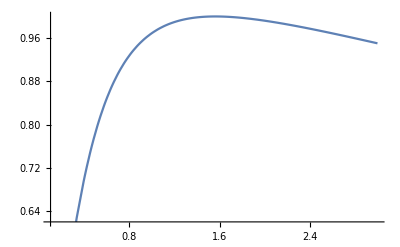

```mathematica
Plot[OverlapIsing[β],{β,0.1,3}]
```

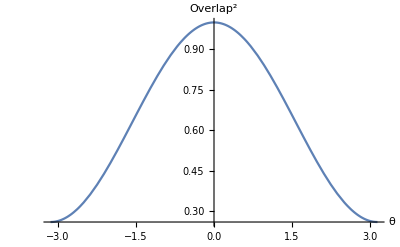

```mathematica
IsingOverlap=Plot[OverlapIsing[βt,θ],{θ,-π,π},PlotRange->All,TicksStyle->Directive[Black,12],AxesLabel->{Style["θ",FontSize->16,Black],Style["Overlap^2",FontSize->16,Black]}]
```

```mathematica
Export["IsingOverlap2.pdf",IsingOverlap]
```

IsingOverlap2.pdf

```mathematica
Plot3D[OverlapIsing[β,θ],{β,1,3},{θ,-π/4,π/4}]
```

-Graphics3D-

```mathematica
6.827751297076589/8.426275476897139 Eigenvalues[HkitModL]//Sort
```

{-6.82775,-6.2162,-4.72477,-4.11322,-2.67494,-2.06339,-0.57196,-0.0395883,0.0395883,0.57196,2.06339,2.67494,4.11322,4.72477,6.2162,6.82775}

```mathematica
Exp[-Sort[ModEshift]]
```

{923.113+0. ⅈ,513.046+0. ⅈ,121.298+0. ⅈ,67.4147+0. ⅈ,15.7167+0. ⅈ,8.73503+0. ⅈ,2.06519+0. ⅈ,1.14779+0. ⅈ,0.87124+0. ⅈ,0.484217+0. ⅈ,0.114482+0. ⅈ,0.0636264+0. ⅈ,0.0148336+0. ⅈ,0.00824418+0. ⅈ,0.00194914+0. ⅈ,0.00108329+0. ⅈ}

```mathematica
(Exp[-Sort[ModEshift]].Exp[-Sort[Ra*Eigenvalues[HkitModL]]])^2/(Exp[-Sort[ModEshift]].Exp[-Sort[ModEshift]]*Exp[-Sort[Ra*Eigenvalues[HkitModL]]].Exp[-Sort[Ra*Eigenvalues[HkitModL]]])
```

0.99981+0. ⅈ

```mathematica
Sort[ModEshift]
```

{-6.82775+0. ⅈ,-6.24037+0. ⅈ,-4.79825+0. ⅈ,-4.21086+0. ⅈ,-2.75473+0. ⅈ,-2.16734+0. ⅈ,-0.725223+0. ⅈ,-0.137837+0. ⅈ,0.137837+0. ⅈ,0.725223+0. ⅈ,2.16734+0. ⅈ,2.75473+0. ⅈ,4.21086+0. ⅈ,4.79825+0. ⅈ,6.24037+0. ⅈ,6.82775+0. ⅈ}

```mathematica
Ra*Eigenvalues[HkitModL]//Sort
```

{-6.82775,-6.2162,-4.72477,-4.11322,-2.67494,-2.06339,-0.57196,-0.0395883,0.0395883,0.57196,2.06339,2.67494,4.11322,4.72477,6.2162,6.82775}

```mathematica
t4=ⅈ*({{0, Sin[π/4], 0, 0}, {-Sin[π/4], 0, Sin[(2π)/4], 0}, {0, -Sin[(2π)/4], 0, Sin[(3π)/4]}, {0, 0, -Sin[(3π)/4], 0}})//Normal;
```

```mathematica
Det[{{0,1/(√2),0,0},{-1/(√2),0,1,0},{0,-1,0,1/(√2)},{0,0,-1/(√2),0}}]
```

```mathematica
Eigenvalues[t4]
```

{1/2 (-1-√3),1/2 (1+√3),1/2 (1-√3),1/2 (-1+√3)}

## 4 fermi terms

```mathematica
λ=-0.856/2;
Hint4=- λ *( Sum[ χ[i].χ[i+1].χ[i+3].χ[i+4],{i,1,Ltot-4}]-χ[Ltot-3].χ[Ltot-2].χ[Ltot].χ[1]+χ[Ltot-2].χ[Ltot-1].χ[1].χ[2]+χ[Ltot-1].χ[Ltot].χ[2].χ[3]-χ[Ltot].χ[1].χ[3].χ[4]);
Hdef4=Hkit+Hint4;
```

```mathematica
Eigenvalues[Hdef4]
```

{-104.984,-104.745,-104.634,-104.538,-104.47,-104.35,-104.297,-104.247,-104.142,-104.103,-104.04,-104.011,-103.9,-103.829,-103.729,-103.676,-103.675,-103.615,-103.574,-103.565,-103.542,-103.388,-103.325,-103.299,-103.212,-103.157,-103.079,-103.045,-103.017,-102.996,-102.962,-102.947,-102.932,-102.926,-102.859,-102.854,-102.76,-102.759,-102.72,-102.652,-102.638,-102.637,-102.523,-102.51,-102.463,-102.445,-102.413,-102.386,-102.343,-102.299,-102.261,-102.259,-102.238,-102.225,-102.171,-102.164,-102.153,-102.119,-102.088,-102.058,-102.032,-102.022,-101.962,-101.96,-101.95,-101.915,-101.839,-101.838,-101.758,-101.74,-101.731,-101.726,-101.655,-101.641,-101.619,-101.592,-101.566,-101.559,-101.533,-101.496,-101.491,-101.435,-101.411,-101.394,-101.363,-101.307,-101.305,-101.289,-101.266,-101.251,-101.224,-101.219,-101.181,-101.162,-101.112,-101.103,-101.052,-101.029,-101.019,-101.017,-100.979,-100.939,-100.853,-100.846,-100.843,-100.829,-100.815,-100.786,-100.765,-100.752,-100.738,-100.69,-100.631,-100.61,-100.568,-100.544,-100.474,-100.473,-100.447,-100.444,-100.418,-100.394,-100.375,-100.344,-100.29,-100.257,-100.237,-100.235,-100.17,-100.163,-100.153,-100.08,-100.046,-100.037,-100.005,-99.9972,-99.9965,-99.9221,-99.9178,-99.906,-99.8616,-99.8406,-99.8315,-99.8109,-99.7664,-99.7644,-99.711,-99.6854,-99.6665,-99.6536,-99.5936,-99.5706,-99.5662,-99.5419,-99.5404,-99.4716,-99.4606,-99.4302,-99.3829,-99.3763,-99.3468,-99.3149,-99.2708,-99.2332,-99.2302,-99.2091,-99.1876,-99.1493,-99.0827,-99.0592,-98.9888,-98.9843,-98.9479,-98.9428,-98.8914,-98.8871,-98.8269,-98.8187,-98.7654,-98.74,-98.6942,-98.6781,-98.6517,-98.5624,-98.5316,-98.5272,-98.4383,-98.4137,-98.4059,-98.3197,-98.2984,-98.2892,-98.2885,-98.2564,-98.1934,-98.1159,-98.0682,-98.0434,-98.007,-97.9956,-97.941,-97.939,-97.9238,-97.8309,-97.826,-97.7805,-97.6856,-97.6812,-97.609,-97.6011,-97.5494,-97.4657,-97.4347,-97.391,-97.3648,-97.3109,-97.3053,-97.2342,-97.1627,-97.1606,-97.0735,-97.0254,-96.9882,-96.9645,-96.8923,-96.8318,-96.8233,-96.7231,-96.7177,-96.6051,-96.5221,-96.4941,-96.3961,-96.3362,-96.2969,-96.2694,-96.1672,-96.1552,-96.0474,-95.9928,-95.8215,-95.7246,-95.489,-95.4779,-95.3459,-95.279,-95.0388,-94.7295,-94.6975,-94.4335,-93.954,-93.7266,-93.3348,-93.0777,-92.8564,-92.6233}

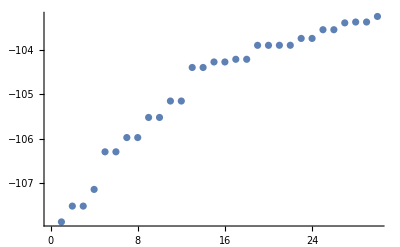

```mathematica
ListPlot[ Take[Eigenvalues[Hdef4],30]//Sort]
```

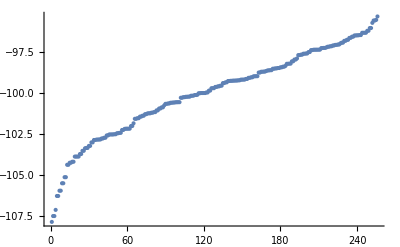

```mathematica
ListPlot[Eigenvalues[Hdef4]//Sort,PlotRange->All]
```